# A simple ML alg to predict Cats will be allowed in your house

### Import the data as a dataset

```mathematica
maindata=Import["C:\\Users\\gurha\\OneDrive\\Documents\\bhoris\\College\\SYBSC\\stat attack\\dataset.csv","Dataset","HeaderLines"->1]
```

Dataset[<>]

### Display the column headers

```mathematica
maindata[Union,Keys]
```

### Define the Objective

```mathematica
objcat="cats_allowed";
```

### Creates a new dataset and assigns an ID to each row

```mathematica
newmaindata=maindata[AssociationThread[Range@Length@#,#]&]
```

Dataset[<>]

### Separates Features and Objective

```mathematica
catdataSplit=newmaindata[All,<|"Features"->Values@*KeyDrop[{objcat}],"Objective"->Key[objcat]|>]
```

Dataset[<>]

### Make a random training set of 3200 entries and use the remaining as test

```mathematica
numTest=800;
ids=Range@newmaindata[Length];
testIds=ids~RandomSample~numTest;
trainIds=ids~Complement~testIds;
dataUnclass=catdataSplit[<|"Test"->testIds,"Train"->trainIds|>];
```

### Training the classifier

```mathematica
classifiertrain=dataUnclass["Train", Classify@*Values,#Features->#Objective&];
```

```mathematica
Information[classifiertrain]
```

Classifier information
Data type | Mixed (number: 12)
Classes | ,,01
Accuracy | (96.11.1) %
Method | LogisticRegression
Single evaluation time | 9.7 ms/example
Batch evaluation speed | 5.43 examples/ms
Loss | 0.132 ± 0.025
Model memory | 418. kB
Training examples used | 3200 examples
Training time | 9.09 s
 |

### Appending classifications in test dataset

```mathematica
dataClass=dataUnclass[{"Test"->Query[All,Append[#,<|"Classified as"->classifiertrain@#Features|>]&]}];
```

### Performance

```mathematica
cfm=dataUnclass["Test",ClassifierMeasurements[classifiertrain,#]&@*Values,#Features->#Objective&];
cfm["Accuracy",ComputeUncertainty->True]
```

0.9450.008

```mathematica
cfm["Precision"]
```

<|0→0.864407,1→0.978723|>

```mathematica
cfm["Specificity"]
```

<|0→0.945205,1→0.944444|>

```mathematica
cfm["Error"]
```

0.055

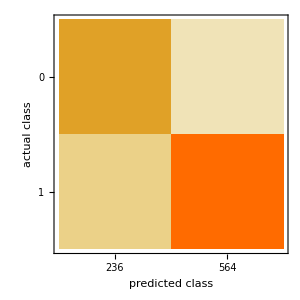

```mathematica
cfm["ConfusionMatrixPlot"]
```

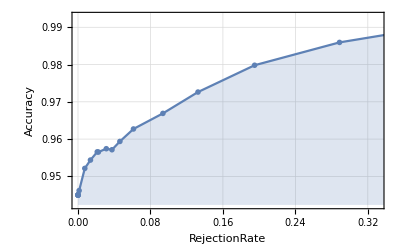

```mathematica
cfm["AccuracyRejectionPlot"]
```

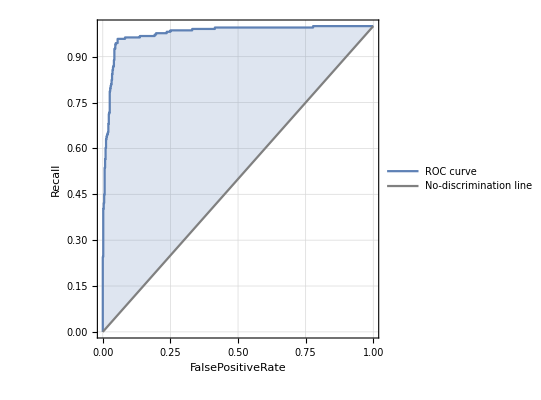
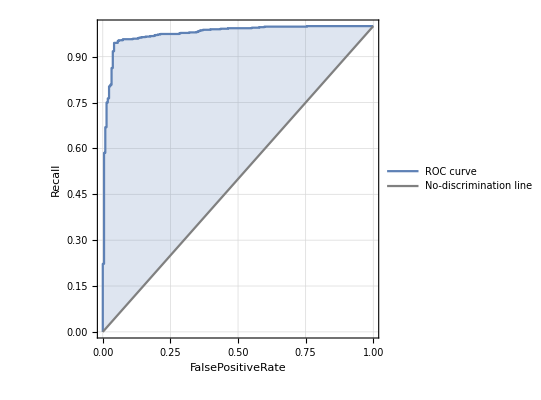
<|0→-Graphics-,1→-Graphics-|>

```mathematica
cfm["ROCCurve"]
```